## Write down the nondimensionalized Fokker-Planck equation

```mathematica
αtfix = 0.005
```

0.005

```mathematica
FP= -λt*D[xt*P[xt, yt], xt]+D[yt*P[xt, yt], yt]-D[xt*P[xt, yt],yt]+(αt^2/2)D[P[xt, yt],{xt,2}]+(αt^2/2)D[P[xt, yt],{yt,2}]/.{αt->αtfix }
```

P[xt,yt]-xt P^(0,1)[xt,yt]+yt P^(0,1)[xt,yt]+0.0000125 P^(0,2)[xt,yt]-λt (P[xt,yt]+xt P^(1,0)[xt,yt])+0.0000125 P^(2,0)[xt,yt]

## Get the steady-state variances

```mathematica
A= {{ -λt,0},{-1, 1}}
B = {{αtfix ,0},{0,αtfix }}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{-λt,0},{-1,1}}

{{0.005,0},{0,0.005}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{-0.0000125/λt,0.0000125/(λt (-1.+1. λt))},{0.0000125/(λt (-1.+1. λt)),-0.0000125/λt+(0.0000125 λt)/(-1.+1. λt)}}

```mathematica
Eigenvectors[A]
```

{{0,1},{1+λt,1}}

```mathematica
Eigenvalues[A]
```

{1,-λt}

```mathematica
Eigenvectors[ss]
```

{{1/2 (-λt^2-√(4+λt^4)),1},{1/2 (-λt^2+√(4+λt^4)),1}}

```mathematica
Eigenvalues[ss]
```

{(αt^2 (2-2 λt+λt^2-√(4+λt^4)))/(4 (-1+λt) λt),(αt^2 (2-2 λt+λt^2+√(4+λt^4)))/(4 (-1+λt) λt)}

## Choose the parameter values

```mathematica
λts = {0.001, 0.002, 0.005, 0.0075, 0.01};
ics = {0.01, 0.02, 0.05, 0.075,0.1};
αArray2 = Flatten[Table[{αtfix},25]]^2
params = Flatten[Table[{λt->l, αtv->a}, {l, λts}, {a, αtvs}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "αtv="<>ToString[a], {l, λts},{a, αtvs}], 1];
```

{0.000025,0.0001,0.0004,0.0025,0.005625,0.000025,0.0001,0.0004,0.0025,0.005625,0.000025,0.0001,0.0004,0.0025,0.005625,0.000025,0.0001,0.0004,0.0025,0.005625,0.000025,0.0001,0.0004,0.0025,0.005625}

{{λt→0.001,αtv→0.005},{λt→0.001,αtv→0.01},{λt→0.001,αtv→0.02},{λt→0.001,αtv→0.05},{λt→0.001,αtv→0.075},{λt→0.002,αtv→0.005},{λt→0.002,αtv→0.01},{λt→0.002,αtv→0.02},{λt→0.002,αtv→0.05},{λt→0.002,αtv→0.075},{λt→0.005,αtv→0.005},{λt→0.005,αtv→0.01},{λt→0.005,αtv→0.02},{λt→0.005,αtv→0.05},{λt→0.005,αtv→0.075},{λt→0.0075,αtv→0.005},{λt→0.0075,αtv→0.01},{λt→0.0075,αtv→0.02},{λt→0.0075,αtv→0.05},{λt→0.0075,αtv→0.075},{λt→0.01,αtv→0.005},{λt→0.01,αtv→0.01},{λt→0.01,αtv→0.02},{λt→0.01,αtv→0.05},{λt→0.01,αtv→0.075}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
cs =Re[N[ Flatten[Table[(eig[[1,1]])^-1/.p, {p, params}]]]]
```

{1.001,1.001,1.001,1.001,1.001,1.00201,1.00201,1.00201,1.00201,1.00201,1.00505,1.00505,1.00505,1.00505,1.00505,1.00761,1.00761,1.00761,1.00761,1.00761,1.01021,1.01021,1.01021,1.01021,1.01021}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xywidths =  N[Table[ss[[1,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
covStds = Sqrt[xywidths]
```

{0.111859,0.11186,0.11186,0.111865,0.111872,0.0791361,0.0791366,0.0791385,0.0791518,0.0791715,0.0501255,0.0501273,0.0501348,0.0501871,0.0502649,0.0409788,0.0409822,0.0409959,0.0410919,0.0412342,0.0355334,0.0355387,0.0355598,0.0357071,0.0359253}

{0.111859,0.112027,0.112694,0.11726,0.123744,0.079136,0.0793725,0.0803119,0.0866025,0.0951972,0.0501248,0.0504975,0.0519615,0.0612372,0.0728869,0.0409776,0.0414327,0.0432049,0.0540062,0.0669266,0.0355317,0.0360555,0.0380789,0.05,0.0637377}

{0.111803,0.111803,0.111803,0.111803,0.111803,0.0790569,0.0790569,0.0790569,0.0790569,0.0790569,0.05,0.05,0.05,0.05,0.05,0.0408248,0.0408248,0.0408248,0.0408248,0.0408248,0.0353553,0.0353553,0.0353553,0.0353553,0.0353553}

```mathematica
θs = ArcTan[cs]
yt0 = 1+5*ytStds*Sin[θs]
xt0 = yt0/cs
```

{0.785899,0.785899,0.785899,0.785899,0.785899,0.786401,0.786401,0.786401,0.786401,0.786401,0.787917,0.787917,0.787917,0.787917,0.787917,0.789191,0.789191,0.789191,0.789191,0.789191,0.790475,0.790475,0.790475,0.790475,0.790475}

{1.39568,1.39627,1.39863,1.41479,1.43772,1.28007,1.28091,1.28423,1.30649,1.33691,1.17766,1.17898,1.18417,1.21705,1.25834,1.14543,1.14704,1.15333,1.19166,1.23752,1.12626,1.12812,1.13531,1.17767,1.22649}

{1.39428,1.39488,1.39723,1.41337,1.43628,1.2775,1.27834,1.28166,1.30387,1.33423,1.17175,1.17306,1.17822,1.21094,1.25202,1.13677,1.13837,1.14461,1.18266,1.22816,1.11488,1.11672,1.12384,1.16577,1.2141}

```mathematica
Δx = 5*Sqrt[αArray2]/Cos[(Pi/2)-θs]
Δy =5*Sqrt[Table[Max[ss[[1,2]]/.p,ss[[2,2]]/.p ],{p,params}]]*Sin[θs]
lrange =ArrayReshape[ Transpose[Table[λts,5]], {1, 25}][[1]]
ΩFunc[Δx_, Δy_, λ_, xt0_, yt0_] :=Parallelogram[{1/2 (1+√(1-4 λ))-Δx, 1}, {{2Δx, 0}, {(yt0-1+Δy)*(1/2 (1+√(1-4 λ))),(yt0-1+Δy)}}]
Ω=MapThread[ΩFunc,{Δx, Δy, lrange,xt0,yt0}];
```

{0.0353376,0.0706753,0.141351,0.353376,0.530065,0.0353199,0.0706399,0.14128,0.353199,0.529799,0.0352666,0.0705332,0.141066,0.352666,0.528999,0.035222,0.070444,0.140888,0.35222,0.52833,0.0351772,0.0703544,0.140709,0.351772,0.527658}

{0.39568,0.396273,0.398634,0.414786,0.437719,0.280068,0.280906,0.28423,0.306493,0.33691,0.177664,0.178985,0.184174,0.217051,0.258342,0.145426,0.147041,0.153331,0.191663,0.237517,0.12626,0.128121,0.135311,0.177672,0.226488}

{0.001,0.001,0.001,0.001,0.001,0.002,0.002,0.002,0.002,0.002,0.005,0.005,0.005,0.005,0.005,0.0075,0.0075,0.0075,0.0075,0.0075,0.01,0.01,0.01,0.01,0.01}

```mathematica
Ω[[1]]
```

Parallelogram[{0.963661,1},{{0.0706753,0},{0.790568,0.791361}}]

```mathematica
Sqrt[αtvs[[1]]^2]
maxCell = Sqrt[αArray2]/8
```

0.005

{0.000625,0.00125,0.0025,0.00625,0.009375,0.000625,0.00125,0.0025,0.00625,0.009375,0.000625,0.00125,0.0025,0.00625,0.009375,0.000625,0.00125,0.0025,0.00625,0.009375,0.000625,0.00125,0.0025,0.00625,0.009375}

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
meshes = MapThread[ToElementMesh[#1, MaxCellMeasure->{"Length"->#2}, MaxBoundaryCellMeasure->{"Length"->#2}]&, {Ω, maxCell}]
```

{ElementMesh[{{0.963661,1.82491},{1.,1.79136}},{TriangleElement[<1046770>]}],ElementMesh[{{0.928324,1.86143},{1.,1.79255}},{TriangleElement[<524010>]}],ElementMesh[{{0.857648,1.93682},{1.,1.79727}},{TriangleElement[<263734>]}],ElementMesh[{{0.645623,2.18112},{1.,1.82957}},{TriangleElement[<109681>]}],ElementMesh[{{0.468934,2.40363},{1.,1.87544}},{TriangleElement[<77024>]}],ElementMesh[{{0.962676,1.59233},{1.,1.56014}},{TriangleElement[<739827>]}],ElementMesh[{{0.927356,1.62932},{1.,1.56181}},{TriangleElement[<370817>]}],ElementMesh[{{0.856716,1.7066},{1.,1.56846}},{TriangleElement[<187797>]}],ElementMesh[{{0.644797,1.96295},{1.,1.61299}},{TriangleElement[<81019>]}],ElementMesh[{{0.468197,2.20027},{1.,1.67382}},{TriangleElement[<59103>]}],ElementMesh[{{0.959708,1.38378},{1.,1.35533}},{TriangleElement[<469053>]}],ElementMesh[{{0.924442,1.42168},{1.,1.35797}},{TriangleElement[<236356>]}],ElementMesh[{{0.853908,1.50254},{1.,1.36835}},{TriangleElement[<121476>]}],ElementMesh[{{0.642309,1.77956},{1.,1.4341}},{TriangleElement[<57314>]}],ElementMesh[{{0.465976,2.03806},{1.,1.51668}},{TriangleElement[<45242>]}],ElementMesh[{{0.957221,1.31632},{1.,1.29085}},{TriangleElement[<383348>]}],ElementMesh[{{0.921999,1.35475},{1.,1.29408}},{TriangleElement[<193947>]}],ElementMesh[{{0.851555,1.43768},{1.,1.30666}},{TriangleElement[<101097>]}],ElementMesh[{{0.640223,1.72509},{1.,1.38333}},{TriangleElement[<50710>]}],ElementMesh[{{0.464113,1.99222},{1.,1.47503}},{TriangleElement[<41567>]}],ElementMesh[{{0.954721,1.27504},{1.,1.25252}},{TriangleElement[<332558>]}],ElementMesh[{{0.919544,1.31391},{1.,1.25624}},{TriangleElement[<168605>]}],ElementMesh[{{0.849189,1.39849},{1.,1.27062}},{TriangleElement[<89054>]}],ElementMesh[{{0.638126,1.69342},{1.,1.35534}},{TriangleElement[<46871>]}],ElementMesh[{{0.46224,1.96596},{1.,1.45298}},{TriangleElement[<39597>]}]}

```mathematica
meshes[[25]]["Wireframe"]
```

-Graphics-

```mathematica
bcs=Table[DirichletCondition[P[xt,yt]==0,ElementMarker==#]&/@m["BoundaryElementMarkerUnion"], {m, meshes}];
```

```mathematica
icPos =Transpose[{xt0, yt0}]
icVar =Table[ss/.p, {p, params}]
ic0 = N[MapThread[PDF[MultinormalDistribution[#1,#2], {xt, yt}]&, {icPos, icVar}]]
```

{{1.39428,1.39568},{1.39488,1.39627},{1.39723,1.39863},{1.41337,1.41479},{1.43628,1.43772},{1.2775,1.28007},{1.27834,1.28091},{1.28166,1.28423},{1.30387,1.30649},{1.33423,1.33691},{1.17175,1.17766},{1.17306,1.17898},{1.17822,1.18417},{1.21094,1.21705},{1.25202,1.25834},{1.13677,1.14543},{1.13837,1.14704},{1.14461,1.15333},{1.18266,1.19166},{1.22816,1.23752},{1.11488,1.12626},{1.11672,1.12812},{1.12384,1.13531},{1.16577,1.17767},{1.2141,1.22649}}

{{{0.0125125,0.0125},{0.0125,0.0125125}},{{0.0125126,0.0125},{0.0125,0.01255}},{{0.0125127,0.0125},{0.0125,0.0127}},{{0.0125138,0.0125},{0.0125,0.01375}},{{0.0125153,0.0125},{0.0125,0.0153125}},{{0.00626253,0.00625},{0.00625,0.0062625}},{{0.0062626,0.00625},{0.00625,0.0063}},{{0.0062629,0.00625},{0.00625,0.00645}},{{0.006265,0.00625},{0.00625,0.0075}},{{0.00626813,0.00625},{0.00625,0.0090625}},{{0.00251256,0.0025},{0.0025,0.0025125}},{{0.00251275,0.0025},{0.0025,0.00255}},{{0.0025135,0.0025},{0.0025,0.0027}},{{0.00251875,0.0025},{0.0025,0.00375}},{{0.00252656,0.0025},{0.0025,0.0053125}},{{0.00167926,0.00166667},{0.00166667,0.00167917}},{{0.00167954,0.00166667},{0.00166667,0.00171667}},{{0.00168067,0.00166667},{0.00166667,0.00186667}},{{0.00168854,0.00166667},{0.00166667,0.00291667}},{{0.00170026,0.00166667},{0.00166667,0.00447917}},{{0.00126262,0.00125},{0.00125,0.0012625}},{{0.001263,0.00125},{0.00125,0.0013}},{{0.0012645,0.00125},{0.00125,0.00145}},{{0.001275,0.00125},{0.00125,0.0025}},{{0.00129062,0.00125},{0.00125,0.0040625}}}

{284.563 2.71828^(0.5 (-1. (-1.39428+xt) (40000. (-1.39428+xt)-39960. (-1.39568+yt))-1. (-39960. (-1.39428+xt)+40000. (-1.39568+yt)) (-1.39568+yt))),179.919 2.71828^(0.5 (-1. (-1.39488+xt) (16038.3 (-1.39488+xt)-15974.4 (-1.39627+yt))-1. (-15974.4 (-1.39488+xt)+15990.4 (-1.39627+yt)) (-1.39627+yt))),97.5605 2.71828^(0.5 (-1. (-1.39723+xt) (4772.12 (-1.39723+xt)-4696.97 (-1.39863+yt))-1. (-4696.97 (-1.39723+xt)+4701.74 (-1.39863+yt)) (-1.39863+yt))),40.022 2.71828^(0.5 (-1. (-1.41337+xt) (869.479 (-1.41337+xt)-790.436 (-1.41479+yt))-1. (-790.436 (-1.41337+xt)+791.305 (-1.41479+yt)) (-1.41479+yt))),26.7532 2.71828^(0.5 (-1. (-1.43628+xt) (432.67 (-1.43628+xt)-353.2 (-1.43772+yt))-1. (-353.2 (-1.43628+xt)+353.633 (-1.43772+yt)) (-1.43772+yt))),402.231 2.71828^(0.5 (-1. (-1.2775+xt) (39999.9 (-1.2775+xt)-39920.1 (-1.28007+yt))-1. (-39920.1 (-1.2775+xt)+40000.1 (-1.28007+yt)) (-1.28007+yt))),254.24 2.71828^(0.5 (-1. (-1.27834+xt) (16076.3 (-1.27834+xt)-15948.8 (-1.28091+yt))-1. (-15948.8 (-1.27834+xt)+15980.9 (-1.28091+yt)) (-1.28091+yt))),137.839 2.71828^(0.5 (-1. (-1.28166+xt) (4837.97 (-1.28166+xt)-4687.95 (-1.28423+yt))-1. (-4687.95 (-1.28166+xt)+4697.63 (-1.28423+yt)) (-1.28423+yt))),56.5354 2.71828^(0.5 (-1. (-1.30387+xt) (946.372 (-1.30387+xt)-788.644 (-1.30649+yt))-1. (-788.644 (-1.30387+xt)+790.536 (-1.30649+yt)) (-1.30649+yt))),37.7845 2.71828^(0.5 (-1. (-1.33423+xt) (510.783 (-1.33423+xt)-352.264 (-1.33691+yt))-1. (-352.264 (-1.33423+xt)+353.285 (-1.33691+yt)) (-1.33691+yt))),635.03 2.71828^(0.5 (-1. (-1.17175+xt) (39999.5 (-1.17175+xt)-39800.5 (-1.17766+yt))-1. (-39800.5 (-1.17175+xt)+40000.5 (-1.17766+yt)) (-1.17766+yt))),401.017 2.71828^(0.5 (-1. (-1.17306+xt) (16189.2 (-1.17306+xt)-15871.8 (-1.17898+yt))-1. (-15871.8 (-1.17306+xt)+15952.7 (-1.17898+yt)) (-1.17898+yt))),217.298 2.71828^(0.5 (-1. (-1.17822+xt) (5033.09 (-1.17822+xt)-4660.27 (-1.18417+yt))-1. (-4660.27 (-1.17822+xt)+4685.43 (-1.18417+yt)) (-1.18417+yt))),89.0356 2.71828^(0.5 (-1. (-1.21094+xt) (1173.59 (-1.21094+xt)-782.396 (-1.21705+yt))-1. (-782.396 (-1.21094+xt)+788.264 (-1.21705+yt)) (-1.21705+yt))),59.4277 2.71828^(0.5 (-1. (-1.25202+xt) (740.69 (-1.25202+xt)-348.56 (-1.25834+yt))-1. (-348.56 (-1.25202+xt)+352.264 (-1.25834+yt)) (-1.25834+yt))),776.778 2.71828^(0.5 (-1. (-1.13677+xt) (39998.9 (-1.13677+xt)-39701.1 (-1.14543+yt))-1. (-39701.1 (-1.13677+xt)+40001.1 (-1.14543+yt)) (-1.14543+yt))),490.148 2.71828^(0.5 (-1. (-1.13837+xt) (16281.7 (-1.13837+xt)-15807.5 (-1.14704+yt))-1. (-15807.5 (-1.13837+xt)+15929.6 (-1.14704+yt)) (-1.14704+yt))),265.455 2.71828^(0.5 (-1. (-1.14461+xt) (5192.88 (-1.14461+xt)-4636.5 (-1.15333+yt))-1. (-4636.5 (-1.14461+xt)+4675.45 (-1.15333+yt)) (-1.15333+yt))),108.615 2.71828^(0.5 (-1. (-1.18266+xt) (1358.4 (-1.18266+xt)-776.228 (-1.19166+yt))-1. (-776.228 (-1.18266+xt)+786.416 (-1.19166+yt)) (-1.19166+yt))),72.3583 2.71828^(0.5 (-1. (-1.22816+xt) (925.836 (-1.22816+xt)-344.497 (-1.23752+yt))-1. (-344.497 (-1.22816+xt)+351.441 (-1.23752+yt)) (-1.23752+yt))),895.826 2.71828^(0.5 (-1. (-1.11488+xt) (39998. (-1.11488+xt)-39602. (-1.12626+yt))-1. (-39602. (-1.11488+xt)+40002. (-1.12626+yt)) (-1.12626+yt))),564.82 2.71828^(0.5 (-1. (-1.11672+xt) (16372.8 (-1.11672+xt)-15743.1 (-1.12812+yt))-1. (-15743.1 (-1.11672+xt)+15906.8 (-1.12812+yt)) (-1.12812+yt))),305.714 2.71828^(0.5 (-1. (-1.12384+xt) (5350.06 (-1.12384+xt)-4612.12 (-1.13531+yt))-1. (-4612.12 (-1.12384+xt)+4665.62 (-1.13531+yt)) (-1.13531+yt))),124.851 2.71828^(0.5 (-1. (-1.16577+xt) (1538.46 (-1.16577+xt)-769.231 (-1.17767+yt))-1. (-769.231 (-1.16577+xt)+784.615 (-1.17767+yt)) (-1.17767+yt))),82.9578 2.71828^(0.5 (-1. (-1.2141+xt) (1103.74 (-1.2141+xt)-339.613 (-1.22649+yt))-1. (-339.613 (-1.2141+xt)+350.65 (-1.22649+yt)) (-1.22649+yt)))}

General::munfl: 1/2.71828^5768.45 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^2326.84 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^708.846 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

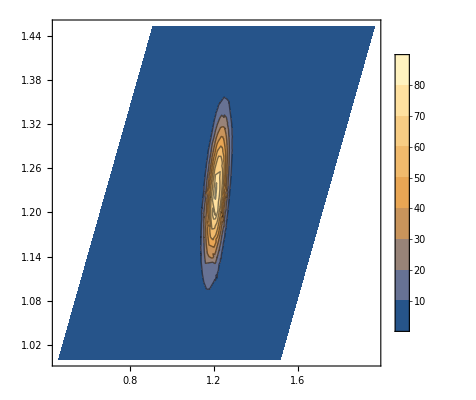

```mathematica
toPlot=25;
ContourPlot[ic0[[toPlot]], {xt,yt}∈Ω[[toPlot]], PlotRange->{0,100}, PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement"}] ;
Print["test"];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes}];
```

test

test

test

«22 more identical outputs»

```mathematica
dv = Table[Derivative[0,1][sol], {sol, solsIc0}];
```

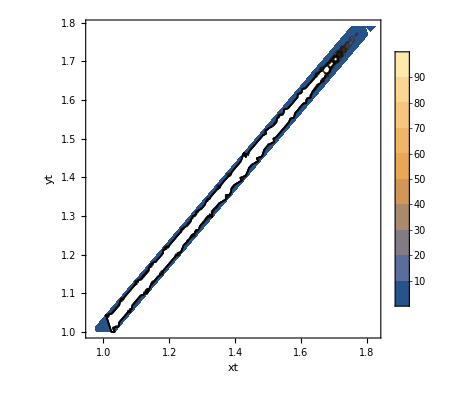

```mathematica
toPlot=1;
ContourPlot[solsIc0[[toPlot]][xt, yt], {xt,yt}∈Ω[[toPlot]], AxesLabel->{xt, yt}, PlotRange->{0, 100}, PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{dv,Table[1, 25]}])*(αArray2/2);
bounds = Transpose[{1/cs-Δx, 1/cs+Δx}];
```

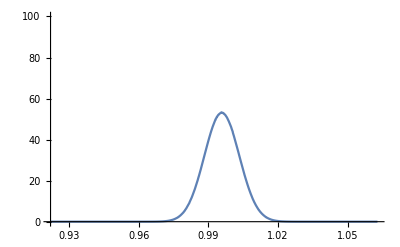

```mathematica
Plot[XIc0[[17]], {xt,bounds[[17, 1]], bounds[[17, 2]]}, PlotLegends->legend[[17]], PlotRange->{-0.1, 100}]
```

```mathematica
IntegFunc[f_, bound_] :=NIntegrate[f, {xt, bound[[1]], bound[[2]]}]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0,bounds}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {corrected*xt,bounds}]
secondIc0 = MapThread[IntegFunc, {corrected*xt*xt,bounds}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00121}. NIntegrate obtained 0.999535 and 0.0000619734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00535}. NIntegrate obtained 0.999518 and 0.000078266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.03765}. NIntegrate obtained 0.998279 and 0.000125437 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.999535,0.999518,0.998279,0.996712,0.993269,0.999254,0.999816,0.998907,0.996567,0.993067,0.998163,0.999889,0.999691,0.99755,0.99549,0.996623,0.99981,0.999868,0.998126,0.996461,0.994534,0.999538,0.999985,0.998822,0.996977}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00121}. NIntegrate obtained 0.998994 and 0.0000620073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00535}. NIntegrate obtained 1.00586 and 0.0000789425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.03765}. NIntegrate obtained 1.0221 and 0.000137426 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.998994,1.00586,1.0221,1.07821,1.12843,0.997989,1.00401,1.01844,1.06898,1.11462,0.994966,0.999268,1.01041,1.052,1.09074,0.992436,0.995865,1.00532,1.04242,1.07778,0.989892,0.992719,1.00095,1.03457,1.06753}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00121}. NIntegrate obtained 0.998014 and 0.0000620175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00535}. NIntegrate obtained 1.01181 and 0.0000796026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.03765}. NIntegrate obtained 1.04482 and 0.000145435 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.998014,1.01181,1.04482,1.16301,1.2742,0.99601,1.00809,1.03736,1.1432,1.24326,0.989982,0.998623,1.02106,1.10728,1.19076,0.984953,0.991799,1.01082,1.08726,1.1628,0.979911,0.985548,1.00206,1.07112,1.14069}

{0.0000249561,0.0000534913,0.000130006,0.000461885,0.000846912,0.0000280099,0.000056615,0.000131132,0.000482096,0.000890945,0.0000246376,0.0000860002,0.000144263,0.000580119,0.00104584,0.0000249719,0.0000517384,0.000150154,0.000616662,0.00119773,0.0000249736,0.0000575747,0.000159167,0.000782206,0.00107934}

```mathematica
grid = Flatten[Table[{l, a}, {l, λts}, {a, αtvs}], 1];
params
```

{{λt→0.001,αtv→0.005},{λt→0.001,αtv→0.01},{λt→0.001,αtv→0.02},{λt→0.001,αtv→0.05},{λt→0.001,αtv→0.075},{λt→0.002,αtv→0.005},{λt→0.002,αtv→0.01},{λt→0.002,αtv→0.02},{λt→0.002,αtv→0.05},{λt→0.002,αtv→0.075},{λt→0.005,αtv→0.005},{λt→0.005,αtv→0.01},{λt→0.005,αtv→0.02},{λt→0.005,αtv→0.05},{λt→0.005,αtv→0.075},{λt→0.0075,αtv→0.005},{λt→0.0075,αtv→0.01},{λt→0.0075,αtv→0.02},{λt→0.0075,αtv→0.05},{λt→0.0075,αtv→0.075},{λt→0.01,αtv→0.005},{λt→0.01,αtv→0.01},{λt→0.01,αtv→0.02},{λt→0.01,αtv→0.05},{λt→0.01,αtv→0.075}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {5,5}];
varArrayIc0 = ArrayReshape[varsIc0, {5,5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5,5}];
diffArrayIc0 = ArrayReshape[diffIc0,{5,5}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{2,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5}, λts}];
yticks = Transpose[{{1, 2, 3, 4, 5}, αtvs}];
```

```mathematica
ArrayPlot[Sqrt[varArrayIc0], ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[Sqrt[varArrayIc0]],5]]
Grid[N[Reverse[normArrayIc0],5]]
```

-Graphics-

0.00499736 | 0.0075878 | 0.0126161 | 0.027968 | 0.0328533
0.00499719 | 0.00719294 | 0.0122537 | 0.0248327 | 0.0346083
0.00496363 | 0.00927363 | 0.0120109 | 0.0240857 | 0.0323395
0.00529244 | 0.0075243 | 0.0114513 | 0.0219567 | 0.0298487
0.00499561 | 0.00731378 | 0.011402 | 0.0214915 | 0.0291018

0.994534 | 0.999538 | 0.999985 | 0.998822 | 0.996977
0.996623 | 0.99981 | 0.999868 | 0.998126 | 0.996461
0.998163 | 0.999889 | 0.999691 | 0.99755 | 0.99549
0.999254 | 0.999816 | 0.998907 | 0.996567 | 0.993067
0.999535 | 0.999518 | 0.998279 | 0.996712 | 0.993269

```mathematica
ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[meanArrayIc0],5]]
```

-Graphics-

0.989892 | 0.992719 | 1.00095 | 1.03457 | 1.06753
0.992436 | 0.995865 | 1.00532 | 1.04242 | 1.07778
0.994966 | 0.999268 | 1.01041 | 1.052 | 1.09074
0.997989 | 1.00401 | 1.01844 | 1.06898 | 1.11462
0.998994 | 1.00586 | 1.0221 | 1.07821 | 1.12843

```mathematica
Grid[1/Reverse[ArrayReshape[cs, {5, 5}]]]
```

0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898
0.992443 | 0.992443 | 0.992443 | 0.992443 | 0.992443
0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975
0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996
0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999

```mathematica
Table[(1+Sqrt[1-4l])/2, {l, {0.05, 0.08, 0.1, 0.15,0.2}}]
```

{0.947214,0.912311,0.887298,0.816228,0.723607}

```mathematica
f1 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, %210}]]
```

InterpolatingFunction[…]

```mathematica
f2 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.09,1.01, 0.97,0.86,0.74 }-%210}]]
```

InterpolatingFunction[…]

```mathematica
f3 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.09, 1.01, 0.97, 0.86, 0.74}}]]
```

InterpolatingFunction[…]

```mathematica
f4 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.04, 0.98, 0.94, 0.84, 0.73}}]]
```

InterpolatingFunction[…]

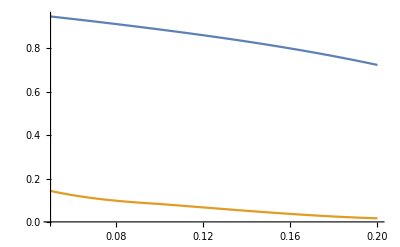

```mathematica
Plot[{f1[x], f2[x]}, {x, 0.05, 0.2}]
```

```mathematica
ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{{ 0,White},{3,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[diffArrayIc0],4]]
```

-Graphics-

-0.000953224 | 0.00319174 | 0.012927 | 0.0530549 | 0.123451
0.000445732 | 0.0027794 | 0.0112394 | 0.0456622 | 0.104291
0.000416853 | 0.00262419 | 0.0104487 | 0.0420214 | 0.0967817
0.000416854 | 0.00254727 | 0.0103964 | 0.0406542 | 0.0924427
0.000396373 | 0.00254852 | 0.0100826 | 0.0404404 | 0.0913144